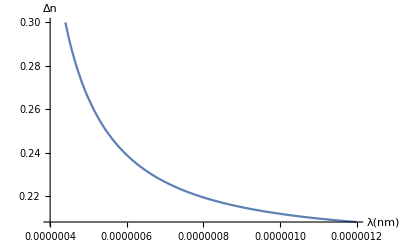

```mathematica
(*Constants*)
c=3*10^8;
d=10^-5; 
f=10^15;
(*Anisotropy fit*)
dn0=0.2002;
lam0=327.44*10^-9;
dn=(dn0*lam)/Sqrt[lam^2-lam0^2];
Plot[dn,{lam,400*10^-9,1200*10^-9},AxesLabel->{λ[nm],Δn}]
(*Phase calc*)
phi=(2*Pi*d/lam)*dn;
(*GVD calc*)
dphi=D[phi,lam];
d2phi=D[dphi,lam];
ddn=D[D[dn,lam],lam];
```

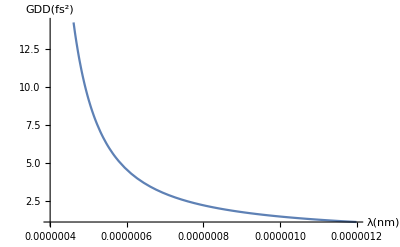

-Graphics-

```mathematica
gvd=(lam^4/(4*Pi^2*c^2))*(d2phi+(2/lam)*dphi);
gvd2=(lam^3/(2*Pi*c^2))*(ddn)*d;
Plot[gvd*f^2,{lam,400*10^-9,1200*10^-9},AxesLabel->{λ[nm],GDD[fs^2]}]
Plot[gvd2*f^2,{lam,400*10^-9,1200*10^-9},AxesLabel->{λ[nm],GDD[fs^2]}]
```